# Generation of test data for Cu d-Hamiltonian

```mathematica
Needs["GroupTheory`"];
```

```mathematica
dir=NotebookDirectory[];
```

```mathematica
SetDirectory[dir];
```

## d-Hamiltonian

Read Hamiltonian from file.

```mathematica
hfcc=GTReadFromFile["fcc_d.ham"];
```

All necessary data are available   in the notebook directory.

```mathematica
cu=GTTbDatabaseRetrieve["TB_Handbook","Cu"]
```

{{(ssσ)_1,-0.07518},{(spσ)_1,0.11571},{(ppσ)_1,0.19669},{(ppπ)_1,0.0194},{(sdσ)_1,-0.03107},{(pdσ)_1,-0.03289},{(pdπ)_1,0.01753},{(ddσ)_1,-0.02566},{(ddπ)_1,0.018},{(ddδ)_1,-0.00408},{(ssσ)_2,-0.00092},{(spσ)_2,0.01221},{(ppσ)_2,0.05389},{(ppπ)_2,0.00846},{(sdσ)_2,-0.00852},{(pdσ)_2,-0.00536},{(pdπ)_2,0.00321},{(ddσ)_2,-0.00451},{(ddπ)_2,0.00241},{(ddδ)_2,-0.00029},{(ss0),0.79466},{(pp0),1.35351},{(dd0),0.37},{(dd1),0.37307},{(dd2),0.3718},{(pd0),0.}}

```mathematica
GTTbPrintParmSet["TB_Handbook","Cu"];
```

Name       : | Cu
Structure  : | fcc
Authors    : | Papaconstantopoulos
Reference  : | Handbook of the Bandstructure of Elemental Solids, Springer, 1986

(ssσ)_1 | (spσ)_1 | (ppσ)_1 | (ppπ)_1 | (sdσ)_1 | (pdσ)_1 | (pdπ)_1 | (ddσ)_1 | (ddπ)_1 | (ddδ)_1
-0.07518 | 0.11571 | 0.19669 | 0.0194 | -0.03107 | -0.03289 | 0.01753 | -0.02566 | 0.018 | -0.00408

(ssσ)_2 | (spσ)_2 | (ppσ)_2 | (ppπ)_2 | (sdσ)_2 | (pdσ)_2 | (pdπ)_2 | (ddσ)_2 | (ddπ)_2 | (ddδ)_2
-0.00092 | 0.01221 | 0.05389 | 0.00846 | -0.00852 | -0.00536 | 0.00321 | -0.00451 | 0.00241 | -0.00029

(ss0) | (pp0) | (dd0) | (dd1) | (dd2) | (pd0)
0.79466 | 1.35351 | 0.37 | 0.37307 | 0.3718 | 0.

## Band structure

the parameter set is restrict to the parameters appearing in the Hamiltonian

```mathematica
cu1={{Subscript["(ddσ)", 1],-0.02566},{Subscript["(ddπ)", 1],0.018},{Subscript["(ddδ)", 1],-0.00408},{Subscript["(ddσ)", 2],-0.00451},{Subscript["(ddπ)", 2],0.00241},{Subscript["(ddδ)", 2],-0.00029},{"(dd0)",0.37}}
```

{{(ddσ)_1,-0.02566},{(ddπ)_1,0.018},{(ddδ)_1,-0.00408},{(ddσ)_2,-0.00451},{(ddπ)_2,0.00241},{(ddδ)_2,-0.00029},{(dd0),0.37}}

export the original parameters

```mathematica
parm1=GTTbParmExport[cu1,"cu_d.parm","Cu-d Papa",hfcc]
```

1 | 2 | 3 | 4 | 5 | 6 | 7
(ddσ)_1 | (ddπ)_1 | (ddδ)_1 | (ddσ)_2 | (ddπ)_2 | (ddδ)_2 | (dd0)
-0.02566 | 0.018 | -0.00408 | -0.00451 | 0.00241 | -0.00029 | 0.37

{{(ddσ)_1,-0.02566},{(ddπ)_1,0.018},{(ddδ)_1,-0.00408},{(ddσ)_2,-0.00451},{(ddπ)_2,0.00241},{(ddδ)_2,-0.00029},{(dd0),0.37}}

```mathematica
GTWriteToFile["parm0.parm",parm1]
```

parametrize Hamiltonian

```mathematica
hfccp= hfcc /. GTTbParmToRule[cu1];
```

calculate band structure

Maximum Abscissa = 4.48735

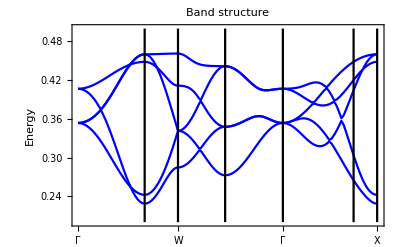

```mathematica
kp=GTBZPath["fcc"];
plt1=GTBandStructure[hfccp,kp,30,5, Joined->True,PlotStyle->Blue,PlotRange->{{0,4.5},{.2,.5}}]
```

## Export band structure data

export the data for fit with least square method. For other fit methods those datasets are the same

```mathematica
SetDirectory[dir<>"../fit/lsqr"];
```

### Definition of k-points

```mathematica
kp=GTBZPath["fcc"];kpsym=kp[[1]];
```

```mathematica
kpl=GTBZLines[kp,{5,5,5,5,5,5}];kpline=Transpose[kpl[[1]]][[3]];
```

### Symmetry points

```mathematica
bands0=GTBands[hfccp,kpsym,5,GOPlotBands->False,GOVerbose->True];
```

k-point | Eigenvalues |  |  |  | 
{0,0,0} |  0.3537 |  0.3537 |  0.3537 |  0.4067 |  0.4068
{0,0,1} |  0.2287 |  0.2423 |  0.4485 |  0.4601 |  0.4601
{0,1/2,1} |  0.2848 |  0.3416 |  0.3416 |  0.4115 |  0.4613
{1/2,1/2,1/2} |  0.2726 |  0.3478 |  0.3478 |  0.4417 |  0.4417
{0,0,0} |  0.3537 |  0.3537 |  0.3537 |  0.4067 |  0.4068
{3/4,3/4,0} |  0.2649 |  0.3037 |  0.4043 |  0.4202 |  0.4485
{1,1,0} |  0.2287 |  0.2423 |  0.4485 |  0.4601 |  0.4601

```mathematica
GTTbFitExport["energ.sy",bands0]
```

number of k-points = 7

number of bands    = 5

energ.sy

### Symmetry lines

```mathematica
bands1=GTBands[hfccp,kpline,5,GOPlotBands->False,GOVerbose->True];
```

k-point | Eigenvalues |  |  |  | 
{0,0,0} |  0.3537 |  0.3537 |  0.3537 |  0.4067 |  0.4068
{0,0,1/4} |  0.3380 |  0.3644 |  0.3644 |  0.3897 |  0.4134
{0,0,1/2} |  0.2992 |  0.3357 |  0.3973 |  0.3973 |  0.4288
{0,0,3/4} |  0.2592 |  0.2638 |  0.4397 |  0.4397 |  0.4429
{0,0,1} |  0.2287 |  0.2423 |  0.4485 |  0.4601 |  0.4601
{0,1/8,1} |  0.2356 |  0.2492 |  0.4443 |  0.4504 |  0.4603
{0,1/4,1} |  0.2537 |  0.2694 |  0.4234 |  0.4330 |  0.4607
{0,3/8,1} |  0.2747 |  0.3013 |  0.3847 |  0.4188 |  0.4611
{0,1/2,1} |  0.2848 |  0.3416 |  0.3416 |  0.4115 |  0.4613
{1/8,1/2,7/8} |  0.2940 |  0.3319 |  0.3563 |  0.4073 |  0.4528
{1/4,1/2,3/4} |  0.3088 |  0.3162 |  0.3857 |  0.3917 |  0.4438
{3/8,1/2,5/8} |  0.2839 |  0.3386 |  0.3586 |  0.4270 |  0.4419
{1/2,1/2,1/2} |  0.2726 |  0.3478 |  0.3478 |  0.4417 |  0.4417
{3/8,3/8,3/8} |  0.2845 |  0.3532 |  0.3532 |  0.4320 |  0.4320
{1/4,1/4,1/4} |  0.3132 |  0.3632 |  0.3632 |  0.4118 |  0.4118
{1/8,1/8,1/8} |  0.3418 |  0.3602 |  0.3602 |  0.4045 |  0.4045
{0,0,0} |  0.3537 |  0.3537 |  0.3537 |  0.4067 |  0.4068
{3/16,3/16,0} |  0.3378 |  0.3605 |  0.3651 |  0.3966 |  0.4096
{3/8,3/8,0} |  0.3178 |  0.3490 |  0.3818 |  0.3932 |  0.4163
{9/16,9/16,0} |  0.3109 |  0.3399 |  0.3828 |  0.3890 |  0.4248
{3/4,3/4,0} |  0.2649 |  0.3037 |  0.4043 |  0.4202 |  0.4485
{13/16,13/16,0} |  0.2517 |  0.2778 |  0.4263 |  0.4312 |  0.4536
{7/8,7/8,0} |  0.2406 |  0.2576 |  0.4404 |  0.4443 |  0.4572
{15/16,15/16,0} |  0.2321 |  0.2459 |  0.4464 |  0.4560 |  0.4594
{1,1,0} |  0.2287 |  0.2423 |  0.4485 |  0.4601 |  0.4601

```mathematica
GTTbFitExport["energ.li",bands1]
```

number of k-points = 25

number of bands    = 5

energ.li

## Noisy parameters

### Noise in [-.02,+.02]

```mathematica
rd=RandomReal[{-.02,.02},7]
```

this is the set of random numbers used for the test :

```mathematica
rd={-0.006401069942100324,0.004927356883833084,-0.013616530911724392,-0.005141849921914486,-0.009482848620653524,0.018069610153420054,0.010387163259204371};
```

```mathematica
{pn,parms}=Transpose[cu1];cu1n={pn,parms+rd}//Transpose
```

{{(ddσ)_1,-0.0320611},{(ddπ)_1,0.0229274},{(ddδ)_1,-0.0176965},{(ddσ)_2,-0.00965185},{(ddπ)_2,-0.00707285},{(ddδ)_2,0.0177796},{(dd0),0.380387}}

calculate band structure with noisy parameters

Maximum Abscissa = 4.48735

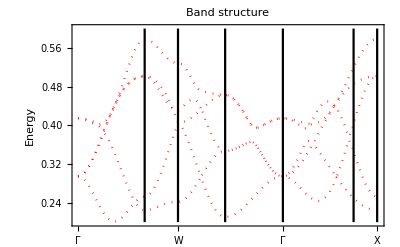

```mathematica
hfccp= hfcc /. GTTbParmToRule[cu1n];
plt2=GTBandStructure[hfccp,kp,30,5, Joined->True,PlotRange->{{0,4.5},{.2,.6}},PlotStyle->{{Red,Dotted}}]
```

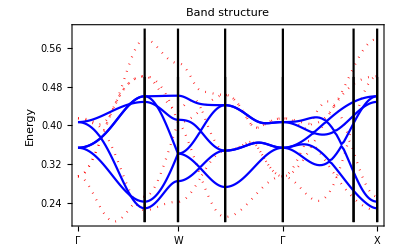

```mathematica
Show[plt2,plt1]
```

export the noisy parameters

```mathematica
parm2=GTTbParmExport[cu1n,"cu_dn1.parm","Cu_d Papa (-0.02,0.02)",hfcc]
```

1 | 2 | 3 | 4 | 5 | 6 | 7
(ddσ)_1 | (ddπ)_1 | (ddδ)_1 | (ddσ)_2 | (ddπ)_2 | (ddδ)_2 | (dd0)
-0.0320611 | 0.0229274 | -0.0176965 | -0.00965185 | -0.00707285 | 0.0177796 | 0.380387

{{(ddσ)_1,-0.0320611},{(ddπ)_1,0.0229274},{(ddδ)_1,-0.0176965},{(ddσ)_2,-0.00965185},{(ddπ)_2,-0.00707285},{(ddδ)_2,0.0177796},{(dd0),0.380387}}

```mathematica
GTWriteToFile["parm1.parm",parm2]
```

### Noise in [-.01,+.01]

```mathematica
rd=RandomReal[{-.01,.01},7]
```

```mathematica
rd1={0.007458871350430503,-0.007070659997946906,0.006259279914108941,-0.006738248826547753,-0.007142206889275891,0.009426398068064522,-0.0035646500891842944};
```

```mathematica
{pn,parms}=Transpose[cu1];cu2n={pn,parms+rd1}//Transpose
```

{{(ddσ)_1,-0.0182011},{(ddπ)_1,0.0109293},{(ddδ)_1,0.00217928},{(ddσ)_2,-0.0112482},{(ddπ)_2,-0.00473221},{(ddδ)_2,0.0091364},{(dd0),0.366435}}

calculate band structure

Maximum Abscissa = 4.48735

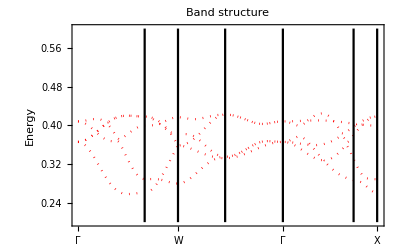

```mathematica
hfccp= hfcc /. GTTbParmToRule[cu2n];
plt2=GTBandStructure[hfccp,kp,30,5, Joined->True,PlotRange->{{0,4.5},{.2,.6}},PlotStyle->{{Red,Dotted}}]
```

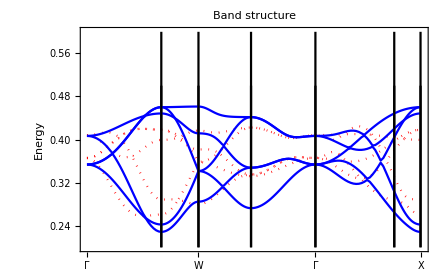

```mathematica
Show[plt2,plt1]
```

```mathematica
parm3=GTTbParmExport[cu2n,"cu_dn2.parm","Cu_d Papa (-0.01,0.01)",hfcc]
```

1 | 2 | 3 | 4 | 5 | 6 | 7
(ddσ)_1 | (ddπ)_1 | (ddδ)_1 | (ddσ)_2 | (ddπ)_2 | (ddδ)_2 | (dd0)
-0.0182011 | 0.0109293 | 0.00217928 | -0.0112482 | -0.00473221 | 0.0091364 | 0.366435

{{(ddσ)_1,-0.0182011},{(ddπ)_1,0.0109293},{(ddδ)_1,0.00217928},{(ddσ)_2,-0.0112482},{(ddπ)_2,-0.00473221},{(ddδ)_2,0.0091364},{(dd0),0.366435}}